## Preparation

```mathematica
(*set 0^0=1*)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];
```

```mathematica
homdirectory=ParentDirectory[NotebookDirectory[]]; (*set home directory here*)
wd=StringJoin[homdirectory,"/GB1/"];
SetDirectory[wd];
figpath=StringJoin[homdirectory, "/figures"];
```

```mathematica
(*create folders*)
Quiet[CreateDirectory[{FileNameJoin[{wd,#}]}]
,CreateDirectory::filex
]&/@{"../figures","output_python","GB1_GE"};
```

### Set parameters

```mathematica
alpha=20;(* alleles per site *)
l=4;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
AA={"K","R","H","E","D","N","Q","T","S","C","G","A","V","L","I","M","P","Y","F","W"} (*the alphabet in amino acids*);
AAtoDigitRules=Table[AA[[i]]->i-1,{i,20}] (*convert amino acids to numbers*);
DigitToAARules=Table[i-1->AA[[i]],{i,20}](*convert numbers to amino acids*);
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences (*list of all possible sequences in amino acids*);
data=Rest[Import["elife-16965-supp1-v4.csv"]]; (*import data*)
logfitness=N[Log[(data[[All,4]]+1/2)/(data[[All,3]]+1/2)]-Log[(data[[1,4]]+1/2)/(data[[1,3]]+1/2)]] (*convert data to logscale with 1/2 as pseudocount to avoid Log[0]. See Wu et al. 2016*);
seq2pos[seq_]:=FromDigits[seq,alpha]+1;(*maps a sequence to its lexicographical order*)
seqlist=(seq2pos[Characters[#]/.AAtoDigitRules])&/@data[[All,1]] (*list of positions for all sequences in the data using lexicographical ordering*);
missing=Complement[Range[1,alpha^l],seqlist]; (*list of positions for all sequences that are missing using lexicographical ordering*)
AB=SparseArray[Transpose[{seqlist,Range[1,Length[seqlist]]}]->1,{alpha^l,Length[seqlist]}]; (*sparse matrix that maps values of all sequences in the data to their lexicographical position. Output is a vector of length alpha^l. *)
response=AB.logfitness;
var=ConstantArray[1,Length[seqlist]]; (*Constant variance for all sequences*)
variance=N[1/(data[[All,3]]+1/2)+1/(data[[All,4]]+1/2)+1/(data[[1,4]]+1/2)+1/(data[[1,4]]+1/2)];
wt=sequences[[seqlist[[1]]]]; (*sequence of the WT*)
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; (*multiplicites of eigenvalues lambda_k, k=0,1,...,l*)
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2);(*Number of faces of the sequence space*)
```

### Export data to other programs

```mathematica
Export["data/seqsGB1.txt",sequences[[seqlist]] ,"CSV"];
Export["data/seqlist.txt",seqlist,"CSV"];
Export["data/var.txt",AB.variance,"CSV"];
Export["data/response.txt",response,"CSV"];
```

### Functions

#### basic functions

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
r2[x_,y_]:=Correlation[x,y]^2;
mse[x_,y_]:=Mean[(x-y)^2];
maxorder[list_]:=Module[{i},For[i=1,list[[i;;]]!=ConstantArray[0,Length[list[[i;;]]]],i++];i-1];
```

```mathematica
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
wkd = Table[w[k,d],{d,0,l},{k,0,l}]; (*Krawtchouk matrix*)
```

```mathematica
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
```

#### regressions

```mathematica
s2dTaylor[seq_,order_,wt_]:=Module[{seqprime,sub1,sub2,pos},
seqprime=Mod[seq-wt,alpha];
sub1=Subsets[seqprime,{order}];
sub2=Table[Join[{i},sub1[[i]]],{i,Length[sub1]}];pos=FromDigits[Rest[#]-1,alpha-1]+1+(#[[1]]-1)*((alpha-1)^order)&/@Select[sub2,!MemberQ[#,0]&];
SparseArray[Table[pos[[i]]->1,{i,Length[pos]}],{Binomial[l,order]*(alpha-1)^order}]
]
```

```mathematica
s2d[seq_,order_]:=Module[{sub1,sub2,pos},
sub1=Subsets[seq,{order}];
sub2=Table[Join[{i},sub1[[i]]],{i,Length[sub1]}];pos=FromDigits[Rest[#],alpha]+1+(#[[1]]-1)*(alpha^order)&/@sub2;
SparseArray[Table[pos[[i]]->1,{i,Length[pos]}],{Binomial[l,order]*(alpha)^order}]
]
```

```mathematica
OrdinaryRegression[design_,response_]:=Module[{cross},
cross=Transpose[design].design;
LinearSolve[cross,Transpose[design].response]]
```

#### Global epistasis

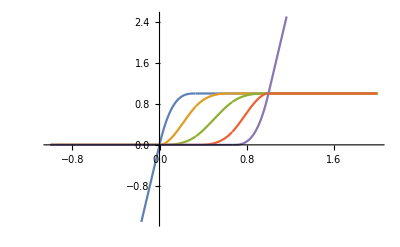

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
Plot[Evaluate[basis],{x,-1,2}]
```

```mathematica
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

#### plotting

```mathematica
labelfigs[figs_]:=Table[
Labeled[figs[[i]],Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}],
{i,Length[figs]}
]
```

```mathematica
ScatterPlot[pd_,true_,plotlab_]:=Show[ListPlot[Transpose@{pd,true},BaseStyle->{FontSize->16},PlotStyle->{{GrayLevel[.2],PointSize[.01]}},PlotRange->{{-20,200},{-20,200}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},FrameLabel->None,PlotLabel->Style[plotlab,Black,FontSize->16],FrameStyle->fstyle],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[pd,true],.01],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[pd,true],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{130,20}]],ImageSize->300]
```

```mathematica
ScatterPlot2[pd_,true_,plotlab_, xlab_, ylab_]:=Show[ListPlot[Transpose@{pd,true},BaseStyle->{FontSize->16},PlotStyle->{{GrayLevel[.2],PointSize[.01]}},
PlotRange->{{-9,3.5},{-9,3.5}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Range[-9,3.5,2],False},{Range[-9,3.5,2],False}},FrameLabel->{xlab,ylab},PlotLabel->Style[plotlab,Black,FontSize->16],FrameStyle->fstyle],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[pd,true],.01],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[pd,true],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{0,-7}]],ImageSize->300]
```

#### Variance component functions

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
(*MakeAdj[A_,l_]:=SparseArray[
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]*)
```

```mathematica
(*Adj=MakeAdj[alpha,l];//AbsoluteTiming*)
```

```mathematica
(*MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
L=MakeLaplacian[alpha,l];//AbsoluteTiming*)
```

```mathematica
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]
```

```mathematica
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;
```

```mathematica
degree=(alpha-1)*l;
```

```mathematica
nbsizes=Table[Binomial[l,p](alpha-1)^p,{p,0,l}]
```

{1,76,2166,27436,130321}

```mathematica
CollapsedAdjEntries[d1_,d2_]:=(1/((alpha-1)*l))If[Abs[d1-d2]>1,0,If[d1==d2,d1(alpha-2),If[d1>d2,(l-d2)(alpha-1),d2]]];
```

```mathematica
NCAdj=Table[CollapsedAdjEntries[d1,d2],{d1,0,l},{d2,0,l}];
```

```mathematica
phisd=NestList[NCAdj.#&,PadRight[{1},l+1],l];
```

```mathematica
AnEntries=Table[degree^s*(phisd[[s+1]]/nbsizes),{s,0,l}];
```

```mathematica
RdCoeffsAn=Table[LinearSolve[Transpose@AnEntries,ReplacePart[ConstantArray[0,l+1],{i->1}]],{i,l+1}];
```

```mathematica
EAC[y_,list_]:=Module[{PresenceAbsence,npairsd,AB},
AB=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{alpha^l,Length[list]}];
PresenceAbsence=AB.ConstantArray[1,Length[list]];
npairsd=Table[PresenceAbsence.(RdCoeffsAn[[i]].NestList[Adj.#&,PresenceAbsence,l]),{i,l+1}];
Table[((AB.y).(RdCoeffsAn[[i]].NestList[Adj.#&,AB.y,l]))/npairsd[[i]],{i,l+1}]]
```

```mathematica
LambdaLS[list_,y_,var_]:=Module[{m,Ab,PresenceAbsence,npairsd,rowmeans,Mmatrix,rhod,a,v,lambdaest,CinLn},
Mmatrix=Table[0,l+1,l+1];
m=Length@list;
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{alpha^l,Length[list]}];
PresenceAbsence=Ab.ConstantArray[1,Length[list]];
npairsd=Table[PresenceAbsence.(RdCoeffsAn[[k]].NestList[Adj.#&,PresenceAbsence,l]),{k,l+1}];
Do[
Mmatrix[[i,j]]=Mmatrix[[j,i]]=npairsd.(wkd[[All,i]]*wkd[[All,j]]),{i,1,l+1},
{j,1,i}
];
rhod=EAC[y,list]-PadRight[{Mean[var]},l+1];
a=Table[npairsd.(wkd[[All,i]]*rhod),{i,l+1}];
v=Array[p,l+1];
lambdaest=(Last@NMinimize[{v.Mmatrix.v-2v.a+(rhod^2).npairsd,v>0},v,Method->{"Automatic"},MaxIterations->10000])[[All,2]];
{rhod,lambdaest}
]
```

```mathematica
GPinterpol[lambdas_,list_,y_,var_]:=Module[
{KerninLn,KbbBy,Alph,Ab,Ai},
Ab=SparseArray[Transpose[{list,Range[Length[list]]}]->1,{alpha^l,Length[list]}];
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],list],Range[alpha^l-Length[list]]}]->1,{alpha^l,alpha^l-Length[list]}];
KerninLn=Inverse[LPs].(wkd[[All,All]].lambdas);
KbbBy[vec_]:=(Transpose[Ab].SprsinLnBy[Ab.vec,KerninLn]+MakeDiagonal[var].vec);
Alph=LinearSolve[KbbBy[#]&,y,Method->{"Krylov",Method->"ConjugateGradient",MaxIterations->10000}];
SprsinLnBy[Ab.Alph,KerninLn]
]
```

```mathematica
VCLS[list_,y_,var_]:=Module[{lambdas},
lambdas=LambdaLS[list,y,var][[2]];
{lambdas,GPinterpol[lambdas,list,y,var]}
]
```

## Sampling

```mathematica
proportions={0.01,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.25,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.924};
nrep=3;
```

#### Export training&test lists

```mathematica
trs = Table[Table[RandomSample[seqlist,Ceiling[proportions[[i]]*alpha^l]],nrep],{i,Length[proportions]}];
tts=Table[Complement[seqlist,trs[[i,j]]],{i,Length@proportions},{j,nrep}];
```

```mathematica
Do[Export[StringJoin["data/tr_",ToString[i],"_",ToString[j],".tsv"], trs[[i,j]]],{i,Length[proportions]},{j,nrep}]
```

## Fit additive models

```mathematica
null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];
```

```mathematica
pds1way=Table[Table[{},nrep],Length[proportions]];
Do[pds1way[[i,j]]=null.OrdinaryRegression[null[[trs[[i,j]]]],response[[trs[[i,j]]]]],{i,Length[proportions]},{j,nrep}];//AbsoluteTiming
```

{77.4084,Null}

## Fit global epistasis models

#### Export data to Julia

```mathematica
SetDirectory[StringJoin[wd,"GB1_GE"]];
```

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

```mathematica
GB1Data=Transpose@{sequencesAA[[seqlist]],logfitness,variance,ConstantArray["GB1",Length[seqlist]]};
```

```mathematica
Do[Export[StringJoin["GB1","_",ToString[i],"_",ToString[j],".txt"],Prepend[GB1Data[[Flatten[Position[seqlist,#]&/@trs[[i,j]]]]],{"mut","f","v","condition"}],"CSV"],{i,Length@proportions},{j,nrep}]
```

Export command lines for Julia

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin["GB1","_",ToString[i],"_",ToString[j],".txt"]],"d = prepdata(dataf, :mut, :sequence, \"VDGV\", :f, cname = :condition, vname = :v)","@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[ToString[i],"_",ToString[j]]]},{i,Length[trs]},{j,nrep}];
```

```mathematica
Export["terminal.txt",Join[{StringReplace["cd(\"#GB1/GB1_GE\")","#"->wd],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

Paste and excecute commandlines in ““terminal.txt””  in Julia

#### read in global epistasis predictions

```mathematica
pdsGE=Table[{},Length[trs],nrep];
```

Predict whole landscape using GlobalEpistasis output

```mathematica
Do[{pdsGE[[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{"GB1"}}],Thread[{Range[l],Characters["VDGV"]}]];FactorMatrix=Table[Join[{GB1Data[[k,4]]},Thread[{Range[l],Characters[GB1Data[[k,1]]]}]],{k,Flatten[Position[seqlist,#]&/@trs[[i,j]]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,20]&/@Effects/.AAtoDigitRules)  -20 +1,b[[2;;Length[b]]],alpha *l];
spline/@Table[s2d[sequences[[i]],1].coeffsAll+b[[1]],{i,alpha^l}]
],Print[{i,j}]},{i,Length[proportions]},{j,nrep}]
```

{1,1}

{1,2}

{1,3}

{2,1}

{2,2}

{2,3}

{3,1}

{9,3}

{10,1}

{10,2}

{10,3}

{11,1}

{11,2}

{11,3}

{12,1}

{12,2}

{12,3}

{13,1}

{13,2}

{13,3}

{14,1}

{14,2}

{14,3}

{15,1}

{15,2}

{15,3}

{16,1}

{16,2}

{16,3}

{17,1}

{17,2}

{17,3}

{18,1}

{18,2}

{18,3}

```mathematica
SetDirectory[wd];
```

```mathematica
pdsGE>> "pdsGE.m";
```

## Elastic net regressions

```mathematica
SetDirectory[StringJoin[wd,"/GB1_glmnet"]];
```

#### Export design matrix to R

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,4}]],{j,Length[sequences]}],2];
design=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*alpha^k,{k,0,4}]}];
```

```mathematica
Export["rules4.tsv",Transpose@{Most[ArrayRules[design]][[All,1]][[All,1]],Most[ArrayRules[design]][[All,1]][[All,2]]},"TSV"];
```

Run .R file
Then read in results to Mathematica by doing the following:

#### Import results from R

```mathematica
pd2wayEN=Table[{},18,3];
Do[pd2wayEN[[i,j]]=Flatten@Import[StringJoin["pd_elasticnet_pairwise_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,6},{j,3}];
```

```mathematica
pd3wayEN2=Table[{},18,3];
Do[pd3wayEN2[[i,j]]=Flatten@Import[StringJoin["pd_elasticnet_threeway_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,18},{j,3}];
```

```mathematica
SetDirectory[wd];
```

## VC predictions using python

import os
os.chdir("/Users/keitokiddo/VC")
import scipy as sp
import sys
sys.path.insert(1, '/Users/keitokiddo/git/vcregression/vcregression')

import vc_regression as vc
import itertools
import os
import csv
import pandas as pd
import numpy as np
import arrow
import scipy as sp

alpha, l = 20, 4
G = alpha**l
bases = np.array(range(alpha))
seqs = list(itertools.product(bases, repeat=l))

vc.preliminary_preparation(alpha, l)

Loading L_sparse ...

0.27 sec

dirin = "GB1/data/"
dirout = "GB1/output_python"

seqlist=pd.read_csv(dirin + "/seqlist.txt", sep=',',header=None).T
seqlist=seqlist.values.tolist()[0]
seqlist=[seqlist[i] - 1 for i in range(len(seqlist))]

response=pd.read_csv(dirin + "/response.txt", sep=',',header=None).T
response=response.values.tolist()[0]
response=np.array(response)

varall=pd.read_csv(dirin + "/var.txt", sep=',',header=None).T
varall=varall.values.tolist()[0]

#import io
#import sys
#text_trap = io.StringIO()
#sys.stdout = text_trap
#sys.stdout = sys.__stdout__

for i in range(18):
    for j in range(3):
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "tr_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1
        lambdas,map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        pd.DataFrame(map).to_csv(dirout + "/map_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None, index = None)
        pd.DataFrame(lambdas).to_csv(dirout + "/lda_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None, index = None)

#### Import python outputs

```mathematica
SetDirectory[StringJoin[wd,"output_python/"]];
```

```mathematica
pdsVC = Table[{},18,3];
```

```mathematica
Do[pdsVC[[i,j]] = Import[StringJoin["map_", ToString[i], "_", ToString[j], ".tsv"]]//Flatten,{i,18},{j,3}];
```

## Analysis and imputation of full landscape

lambdas, map = vc.compute_posterior_mean_ex(np.array(seqs)[seqlist], np.array(response)[seqlist], np.array(varall)[seqlist])

pd.DataFrame(map).to_csv(dirout + "/map_all_data" + ".tsv", header = None, index = None)

pd.DataFrame(lambdas).to_csv(dirout + "/lda_all_data" + ".tsv", header = None, index = None)

## Posterior sampling

vc.lda_star = np.array(pd.read_csv(dirout + '/lda_all_data.tsv', header = None)).flatten()
map = np.array(pd.read_csv(dirout + '/map_all_data.tsv', header = None)).flatten()

vc.set_data_as_global_parameters(np.array(seqs)[seqlist], np.array(response)[seqlist], np.array(varall)[seqlist])
vc.prepare_pos_sampling()
vc.outpath = dirout

start_time = arrow.now().format('YYYY-MM-DD-HH-mm')
vc.start_time = start_time

samples = vc.hamiltonian_monte_carlo(
    n_samples = 2000,
    m = 1,
    initial_position = np.zeros(alpha**l),
    tune = 100,
    initial_step_size = 1e-05,
    num_steps = 100,
    max_energy_change=1000.0
  )

currently working on step 0

initial_potential =  0.0

final_potential =  16769.179882999902

energy_change =  0.1181822891230695

p accept =  0.8885340677549984

current step = 0.0011673311938028249

current acceptance rate = 1.0

currently working on step 1

initial_potential =  16769.179882999902

final_potential =  25033.135507881452

energy_change =  464.1796886282973

p accept =  2.566389780127601e-202

current step = 5.106019975010635e-05

current acceptance rate = 0.5

currently working on step 2

initial_potential =  16769.179882999902

final_potential =  21928.47974523035

energy_change =  0.9741203951707575

p accept =  0.37752427973943714

current step = 2.5906850336761293e-05

current acceptance rate = 0.6666666666666666

currently working on step 3

initial_potential =  21928.47974523035

final_potential =  63713.15445560496

energy_change =  2.025783549179323

p accept =  0.13189046002850885

current step = 3.5451874644056464e-06

current acceptance rate = 0.5

currently working on step 4

initial_potential =  21928.47974523035

final_potential =  23481.136582481282

energy_change =  0.0014250633539631963

p accept =  0.9985759515666522

current step = 5.751649395899416e-05

current acceptance rate = 0.6

currently working on step 5

initial_potential =  23481.136582481282

final_potential =  23829.312352794142

energy_change =  0.07449184395954944

p accept =  0.928215044587561

current step = 0.0005349211331257452

current acceptance rate = 0.6666666666666666

currently working on step 6

initial_potential =  23829.312352794142

final_potential =  28379.79632939194

energy_change =  62.92713993572397

p accept =  4.68910938627659e-28

current step = 4.1632004248287144e-05

current acceptance rate = 0.5714285714285714

currently working on step 7

initial_potential =  23829.312352794142

final_potential =  49868.34825852707

energy_change =  3.2267349395842757

p accept =  0.03968686749523045

current step = 4.582234195140057e-06

current acceptance rate = 0.5

currently working on step 8

initial_potential =  23829.312352794142

final_potential =  26169.90796727709

energy_change =  0.003382275433978066

p accept =  0.996623438016275

current step = 5.194337168206297e-05

current acceptance rate = 0.5555555555555556

currently working on step 9

initial_potential =  26169.90796727709

final_potential =  31058.274747978383

energy_change =  0.9017732965003233

p accept =  0.40584933005366114

current step = 3.4316677543170143e-05

current acceptance rate = 0.6

currently working on step 10

initial_potential =  31058.274747978383

final_potential =  62699.41414284585

energy_change =  2.610196567227831

p accept =  0.07352009070218535

current step = 5.2353654488137275e-06

current acceptance rate = 0.5454545454545454

currently working on step 11

initial_potential =  31058.274747978383

final_potential =  33722.237839012785

energy_change =  0.0050526553532108665

p accept =  0.994960087838496

current step = 4.8750133506910014e-05

current acceptance rate = 0.5833333333333334

currently working on step 12

initial_potential =  33722.237839012785

final_potential =  45171.79616540483

energy_change =  1.8487587229174096

p accept =  0.15743246238789932

current step = 1.1501915989779663e-05

current acceptance rate = 0.6153846153846154

currently working on step 13

initial_potential =  45171.79616540483

final_potential =  52016.71079860492

energy_change =  0.06348822306608781

p accept =  0.9384851717134269

current step = 7.508793704527431e-05

current acceptance rate = 0.6428571428571429

currently working on step 14

initial_potential =  52016.71079860492

final_potential =  60403.38257434206

energy_change =  3.4527509173494764

p accept =  0.03165842676440188

current step = 1.1164017966956578e-05

current acceptance rate = 0.6

currently working on step 15

initial_potential =  52016.71079860492

final_potential =  56270.09119836475

energy_change =  0.03732070926344022

p accept =  0.9633671250393737

current step = 7.447484376212799e-05

current acceptance rate = 0.625

currently working on step 16

initial_potential =  56270.09119836475

final_potential =  60605.95746848993

energy_change =  1.7092407086165622

p accept =  0.18100317460489437

current step = 2.1433946620198633e-05

current acceptance rate = 0.5882352941176471

currently working on step 17

initial_potential =  56270.09119836475

final_potential =  63730.43737102524

energy_change =  0.2504034572048113

p accept =  0.7784866336615448

current step = 6.443537119437593e-05

current acceptance rate = 0.6111111111111112

currently working on step 18

initial_potential =  63730.43737102524

final_potential =  63959.74529751187

energy_change =  0.056946296826936305

p accept =  0.9446447984274491

current step = 0.0003486894840558589

current acceptance rate = 0.631578947368421

currently working on step 19

initial_potential =  63959.74529751187

final_potential =  64703.96715789818

energy_change =  -0.12882989074569196

p accept =  1.1374966090069025

current step = 0.0021850884324733774

current acceptance rate = 0.65

currently working on step 20

initial_potential =  64703.96715789818

final_potential =  103732.29061576653

energy_change =  11396.729742545402

p accept =  0.0

current step = 0.00033423022069943787

current acceptance rate = 0.6190476190476191

currently working on step 21

initial_potential =  64703.96715789818

final_potential =  66815.39085129027

energy_change =  12.659767419740092

p accept =  3.1763830323049895e-06

current step = 5.438925606753527e-05

current acceptance rate = 0.5909090909090909

currently working on step 22

initial_potential =  64703.96715789818

final_potential =  64749.89380147601

energy_change =  0.006996693031396717

p accept =  0.9930277268393201

current step = 0.0003138371079802262

current acceptance rate = 0.6086956521739131

currently working on step 23

initial_potential =  64749.89380147601

final_potential =  66424.75933560106

energy_change =  9.166751708893571

p accept =  0.00010445526034602321

current step = 5.410891935509408e-05

current acceptance rate = 0.5833333333333334

currently working on step 24

initial_potential =  64749.89380147601

final_potential =  64730.35174434418

energy_change =  -0.00579155154991895

p accept =  1.0058083550082995

current step = 0.0003034097573572351

current acceptance rate = 0.6

currently working on step 25

initial_potential =  64730.35174434418

final_potential =  65436.206790391734

energy_change =  1.880984183284454

p accept =  0.1524400030018521

current step = 9.221715412414222e-05

current acceptance rate = 0.5769230769230769

currently working on step 26

initial_potential =  64730.35174434418

final_potential =  66062.59934966313

energy_change =  0.7819895151187666

p accept =  0.45749491223840616

current step = 8.012563174247884e-05

current acceptance rate = 0.5555555555555556

currently working on step 27

initial_potential =  64730.35174434418

final_potential =  66093.61626668723

energy_change =  0.5917761026648805

p accept =  0.553343616373458

current step = 9.577515297977378e-05

current acceptance rate = 0.5714285714285714

currently working on step 28

initial_potential =  66093.61626668723

final_potential =  66463.69573354111

energy_change =  0.20148844085633755

p accept =  0.8175130272560114

current step = 0.00026846575134160835

current acceptance rate = 0.5862068965517241

currently working on step 29

initial_potential =  66463.69573354111

final_potential =  66584.28879127845

energy_change =  -0.6845680880942382

p accept =  1.9829152058706694

current step = 0.001314565843396757

current acceptance rate = 0.6

currently working on step 30

initial_potential =  66584.28879127845

final_potential =  76984.69280638937

energy_change =  918.586904329597

p accept =  0.0

current step = 0.00026183589320144345

current acceptance rate = 0.5806451612903226

currently working on step 31

initial_potential =  66584.28879127845

final_potential =  66494.72751105682

energy_change =  -1.5358516746782698

p accept =  4.645280113151578

current step = 0.0012335416675308887

current acceptance rate = 0.59375

currently working on step 32

initial_potential =  66494.72751105682

final_potential =  69752.93092771029

energy_change =  75.4426766979741

p accept =  1.720528258711663e-33

current step = 0.0002558319068368565

current acceptance rate = 0.5757575757575758

currently working on step 33

initial_potential =  66494.72751105682

final_potential =  67126.65759499901

energy_change =  1.9360057321027853

p accept =  0.14427908971784584

current step = 8.550672921393737e-05

current acceptance rate = 0.5588235294117647

currently working on step 34

initial_potential =  66494.72751105682

final_potential =  66822.11559739022

energy_change =  0.15407922473968938

p accept =  0.8572041065490381

current step = 0.0002514880491778241

current acceptance rate = 0.5714285714285714

currently working on step 35

initial_potential =  66822.11559739022

final_potential =  66961.21785416783

energy_change =  -0.26647779607446864

p accept =  1.3053586049283008

current step = 0.0011052235914538304

current acceptance rate = 0.5833333333333334

currently working on step 36

initial_potential =  66961.21785416783

final_potential =  70799.32421175916

energy_change =  141.1121501213638

p accept =  5.1972292355825555e-62

current step = 0.000246441417305621

current acceptance rate = 0.5675675675675675

currently working on step 37

initial_potential =  66961.21785416783

final_potential =  66862.63843456838

energy_change =  -1.1822180902236141

p accept =  3.261600710052705

current step = 0.0010495611219992957

current acceptance rate = 0.5789473684210527

currently working on step 38

initial_potential =  66862.63843456838

final_potential =  73899.537301843

energy_change =  384.82245872099884

p accept =  7.477039328996759e-168

current step = 0.00024180549724040566

current acceptance rate = 0.5641025641025641

currently working on step 39

initial_potential =  66862.63843456838

final_potential =  67142.6717692155

energy_change =  0.5393864318612032

p accept =  0.5831059178494352

current step = 0.00030384657210786334

current acceptance rate = 0.575

currently working on step 40

initial_potential =  67142.6717692155

final_potential =  67575.91028775249

energy_change =  1.3155218181782402

p accept =  0.26833426500262464

current step = 0.00015603862472338416

current acceptance rate = 0.5609756097560976

currently working on step 41

initial_potential =  67142.6717692155

final_potential =  67365.03955732113

energy_change =  0.3209793361602351

p accept =  0.7254382411748382

current step = 0.000292093291453441

current acceptance rate = 0.5476190476190477

currently working on step 42

initial_potential =  67142.6717692155

final_potential =  67552.0280905745

energy_change =  1.3117934766341932

p accept =  0.269336574104806

current step = 0.0001524705115304381

current acceptance rate = 0.5581395348837209

currently working on step 43

initial_potential =  67552.0280905745

final_potential =  67315.40487824343

energy_change =  -0.4908286552526988

p accept =  1.6336694079508478

current step = 0.0005997894311964501

current acceptance rate = 0.5681818181818182

currently working on step 44

initial_potential =  67315.40487824343

final_potential =  69535.54846576827

energy_change =  38.77328947104979

p accept =  1.4486862479669e-17

current step = 0.00015127303514433398

current acceptance rate = 0.5555555555555556

currently working on step 45

initial_potential =  67315.40487824343

final_potential =  67492.39480975592

energy_change =  0.1946162874228321

p accept =  0.8231504506461638

current step = 0.00036024278449940173

current acceptance rate = 0.5652173913043478

currently working on step 46

initial_potential =  67492.39480975592

final_potential =  68193.44955493306

energy_change =  3.8178418271127157

p accept =  0.02197517598305718

current step = 9.925662318642118e-05

current acceptance rate = 0.5531914893617021

currently working on step 47

initial_potential =  67492.39480975592

final_potential =  67992.69305570303

energy_change =  0.3244750910089351

p accept =  0.7229067143024895

current step = 0.0001791581083400467

current acceptance rate = 0.5625

currently working on step 48

initial_potential =  67992.69305570303

final_potential =  68118.88593233612

energy_change =  0.08656004315707833

p accept =  0.9170804827240745

current step = 0.0005330030485710444

current acceptance rate = 0.5714285714285714

currently working on step 49

initial_potential =  68118.88593233612

final_potential =  68724.55190146923

energy_change =  0.7657855504658073

p accept =  0.46496853122684184

current step = 0.00047965705202791017

current acceptance rate = 0.58

currently working on step 50

initial_potential =  68724.55190146923

final_potential =  68945.64480639991

energy_change =  -0.9391206065192819

p accept =  2.557731176928058

current step = 0.0017214893213244324

current acceptance rate = 0.5882352941176471

currently working on step 51

initial_potential =  68945.64480639991

final_potential =  81492.9872705244

energy_change =  1964.3303554795566

p accept =  0.0

current step = 0.0004673852511036216

current acceptance rate = 0.5769230769230769

currently working on step 52

initial_potential =  68945.64480639991

final_potential =  69310.07898965107

energy_change =  1.3628064100630581

p accept =  0.2559414913435954

current step = 0.0002483300557269893

current acceptance rate = 0.5660377358490566

currently working on step 53

initial_potential =  68945.64480639991

final_potential =  68838.27829518702

energy_change =  -0.578318276500795

p accept =  1.7830373321669106

current step = 0.0008690428858993567

current acceptance rate = 0.5740740740740741

currently working on step 54

initial_potential =  68838.27829518702

final_potential =  70831.34264430903

energy_change =  56.78880131512415

p accept =  2.1723857980866583e-25

current step = 0.0002447980553772347

current acceptance rate = 0.5636363636363636

currently working on step 55

initial_potential =  68838.27829518702

final_potential =  68479.49860482317

energy_change =  -1.8172074722824618

p accept =  6.154647406436079

current step = 0.000840391301314632

current acceptance rate = 0.5714285714285714

currently working on step 56

initial_potential =  68479.49860482317

final_potential =  70222.87511465819

energy_change =  45.88811010692734

p accept =  1.1777334107490933e-20

current step = 0.00024147468905370072

current acceptance rate = 0.5614035087719298

currently working on step 57

initial_potential =  68479.49860482317

final_potential =  68568.56427730093

energy_change =  0.042811751540284604

p accept =  0.9580917323848038

current step = 0.0007346962229349237

current acceptance rate = 0.5689655172413793

currently working on step 58

initial_potential =  68568.56427730093

final_potential =  72331.97262263003

energy_change =  118.15856943541439

p accept =  4.8348756036777376e-52

current step = 0.00021530611380030895

current acceptance rate = 0.559322033898305

currently working on step 59

initial_potential =  68568.56427730093

final_potential =  69079.05300122962

energy_change =  1.3921598845627159

p accept =  0.2485379112889492

current step = 0.00011686667778433766

current acceptance rate = 0.55

currently working on step 60

initial_potential =  68568.56427730093

final_potential =  68558.26646021292

energy_change =  0.00016858166782185435

p accept =  0.999831432541269

current step = 0.00038557746469161707

current acceptance rate = 0.5573770491803278

currently working on step 61

initial_potential =  68558.26646021292

final_potential =  69539.86727367701

energy_change =  7.849633875768632

p accept =  0.00038989469201827564

current step = 0.00011666985220272259

current acceptance rate = 0.5483870967741935

currently working on step 62

initial_potential =  68558.26646021292

final_potential =  68659.58480420709

energy_change =  0.05800017877481878

p accept =  0.9436497787359652

current step = 0.00033161222942397093

current acceptance rate = 0.5555555555555556

currently working on step 63

initial_potential =  68659.58480420709

final_potential =  69058.12767331637

energy_change =  1.7900112165953033

p accept =  0.16695829695288855

current step = 0.0001508272883832143

current acceptance rate = 0.546875

currently working on step 64

initial_potential =  68659.58480420709

final_potential =  69102.5258078892

energy_change =  0.6600542701198719

p accept =  0.5168232856689338

current step = 0.0001564071439356717

current acceptance rate = 0.5538461538461539

currently working on step 65

initial_potential =  69102.5258078892

final_potential =  69056.59149879261

energy_change =  -0.16969571384834126

p accept =  1.1849442343367744

current step = 0.000494808632764469

current acceptance rate = 0.5606060606060606

currently working on step 66

initial_potential =  69056.59149879261

final_potential =  69994.63728760419

energy_change =  12.05516196694225

p accept =  5.8144639110865905e-06

current step = 0.00015548529800324176

current acceptance rate = 0.5522388059701493

currently working on step 67

initial_potential =  69056.59149879261

final_potential =  68812.72673377467

energy_change =  -0.4740137368789874

p accept =  1.6064290541974124

current step = 0.00048457948243763575

current acceptance rate = 0.5588235294117647

currently working on step 68

initial_potential =  68812.72673377467

final_potential =  69121.9787358797

energy_change =  1.3474745251005515

p accept =  0.2598957928337056

current step = 0.00027849602274719886

current acceptance rate = 0.5507246376811594

currently working on step 69

initial_potential =  68812.72673377467

final_potential =  69149.38649520096

energy_change =  1.0973714165738784

p accept =  0.333747214098183

current step = 0.0001903382297775006

current acceptance rate = 0.5571428571428572

currently working on step 70

initial_potential =  69149.38649520096

final_potential =  69134.88710578615

energy_change =  -0.24394219100940973

p accept =  1.2762705484447168

current step = 0.0005798684584380874

current acceptance rate = 0.5633802816901409

currently working on step 71

initial_potential =  69134.88710578615

final_potential =  69680.14871392355

energy_change =  6.599792789726052

p accept =  0.001360649948988088

current step = 0.00018939420206024287

current acceptance rate = 0.5555555555555556

currently working on step 72

initial_potential =  69134.88710578615

final_potential =  69290.14413954204

energy_change =  0.3523551333928481

p accept =  0.7030304080639999

current step = 0.00029540388091248246

current acceptance rate = 0.5616438356164384

currently working on step 73

initial_potential =  69290.14413954204

final_potential =  69286.68621318832

energy_change =  -0.402668745839037

p accept =  1.4958113158649458

current step = 0.0008795770737193463

current acceptance rate = 0.5675675675675675

currently working on step 74

initial_potential =  69286.68621318832

final_potential =  70204.88975679321

energy_change =  5.722776647191495

p accept =  0.0032706169334919006

current step = 0.00029368506201565505

current acceptance rate = 0.56

currently working on step 75

initial_potential =  69286.68621318832

final_potential =  69675.72779858585

energy_change =  1.3954827339039184

p accept =  0.24771342782993402

current step = 0.0001688254817301965

current acceptance rate = 0.5526315789473685

currently working on step 76

initial_potential =  69286.68621318832

final_potential =  69142.91146768528

energy_change =  -0.27117871161317453

p accept =  1.3115094314086266

current step = 0.0004947930615725252

current acceptance rate = 0.5584415584415584

currently working on step 77

initial_potential =  69142.91146768528

final_potential =  70458.7819803179

energy_change =  17.242673512082547

p accept =  3.247895447167426e-08

current step = 0.00016780643015148583

current acceptance rate = 0.5512820512820513

currently working on step 78

initial_potential =  69142.91146768528

final_potential =  69210.22044005324

energy_change =  -0.0018163275090046227

p accept =  1.0018179780309595

current step = 0.0004858331005640044

current acceptance rate = 0.5569620253164557

currently working on step 79

initial_potential =  69210.22044005324

final_potential =  69809.45763333945

energy_change =  6.318177158595063

p accept =  0.0018032275099799735

current step = 0.00016746673097703347

current acceptance rate = 0.55

currently working on step 80

initial_potential =  69210.22044005324

final_potential =  69149.33593440079

energy_change =  -0.23882009845692664

p accept =  1.2697500860353543

current step = 0.0004791457051289509

current acceptance rate = 0.5555555555555556

currently working on step 81

initial_potential =  69149.33593440079

final_potential =  69524.24003864005

energy_change =  1.9646127095329575

p accept =  0.1402101781672231

current step = 0.0002234186900632798

current acceptance rate = 0.5487804878048781

currently working on step 82

initial_potential =  69149.33593440079

final_potential =  69838.58552506095

energy_change =  2.338344164658338

p accept =  0.09648727306628158

current step = 9.589794097721434e-05

current acceptance rate = 0.5421686746987951

currently working on step 83

initial_potential =  69149.33593440079

final_potential =  68876.32518477918

energy_change =  -0.17775146989151835

p accept =  1.1945284080655572

current step = 0.0002705513749961211

current acceptance rate = 0.5476190476190477

currently working on step 84

initial_potential =  68876.32518477918

final_potential =  69362.87660765195

energy_change =  2.162174284167122

p accept =  0.11507464385628112

current step = 0.00012164577821981501

current acceptance rate = 0.5411764705882353

currently working on step 85

initial_potential =  68876.32518477918

final_potential =  68864.87618630711

energy_change =  -0.022397503489628434

p accept =  1.0226502107145898

current step = 0.0003390195272526326

current acceptance rate = 0.5465116279069767

currently working on step 86

initial_potential =  68864.87618630711

final_potential =  69731.7962223865

energy_change =  6.2015896626980975

p accept =  0.002026207088970141

current step = 0.00012189957190664051

current acceptance rate = 0.5402298850574713

currently working on step 87

initial_potential =  68864.87618630711

final_potential =  68949.33089489411

energy_change =  0.05720238364301622

p accept =  0.9444029183211683

current step = 0.0003002512783212025

current acceptance rate = 0.5454545454545454

currently working on step 88

initial_potential =  68949.33089489411

final_potential =  68999.86143748341

energy_change =  -0.24115227541187778

p accept =  1.272714823727235

current step = 0.0008198721745164304

current acceptance rate = 0.550561797752809

currently working on step 89

initial_potential =  68999.86143748341

final_potential =  69645.47100737231

energy_change =  -1.2788232638849877

p accept =  3.592409918882747

current step = 0.002216164184742465

current acceptance rate = 0.5555555555555556

currently working on step 90

initial_potential =  69645.47100737231

final_potential =  73253.63541905186

energy_change =  277.95356212591287

p accept =  1.9333110952605301e-121

current step = 0.0008027171389684664

current acceptance rate = 0.5494505494505495

currently working on step 91

initial_potential =  69645.47100737231

final_potential =  70250.93481697276

energy_change =  5.457047569565475

p accept =  0.004266132629303439

current step = 0.0002962247413391226

current acceptance rate = 0.5434782608695652

currently working on step 92

initial_potential =  69645.47100737231

final_potential =  69672.83310527838

energy_change =  -0.2937610956723802

p accept =  1.34146338397395

current step = 0.000793084349205851

current acceptance rate = 0.5483870967741935

currently working on step 93

initial_potential =  69672.83310527838

final_potential =  72282.33111271955

energy_change =  96.30431844945997

p accept =  1.4981866192734434e-42

current step = 0.0002931028458547418

current acceptance rate = 0.5425531914893617

currently working on step 94

initial_potential =  69672.83310527838

final_potential =  69751.26731894238

energy_change =  0.10342977690743282

p accept =  0.9017393434439278

current step = 0.000641120082015503

current acceptance rate = 0.5473684210526316

currently working on step 95

initial_potential =  69751.26731894238

final_potential =  70209.92487888073

energy_change =  2.29836006462574

p accept =  0.10042339663840189

current step = 0.00029132925672978153

current acceptance rate = 0.5416666666666666

currently working on step 96

initial_potential =  69751.26731894238

final_potential =  69656.85897136883

energy_change =  -0.5326091832248494

p accept =  1.7033709223584959

current step = 0.0007656186594229118

current acceptance rate = 0.5463917525773195

currently working on step 97

initial_potential =  69656.85897136883

final_potential =  70170.00624662563

energy_change =  -0.4016191611299291

p accept =  1.4942421588057833

current step = 0.00199397741747453

current acceptance rate = 0.5510204081632653

currently working on step 98

initial_potential =  70170.00624662563

final_potential =  90339.65359342186

energy_change =  5200.83833410294

p accept =  0.0

current step = 0.0007512577383080891

current acceptance rate = 0.5454545454545454

currently working on step 99

initial_potential =  70170.00624662563

final_potential =  73266.73584367461

energy_change =  107.17804595310008

p accept =  2.839004372430255e-47

current step = 0.00035007130115635466

current acceptance rate = 0.54

currently working on step 100

initial_potential =  70170.00624662563

final_potential =  70307.89791697955

energy_change =  -0.04715405422030017

p accept =  1.0482834891365667

current step = 0.00035007130115635466

current acceptance rate = 0.5445544554455446

currently working on step 101

initial_potential =  70307.89791697955

final_potential =  70604.43573083324

energy_change =  2.228389563038945

p accept =  0.10770173740681113

current step = 0.00035007130115635466

current acceptance rate = 0.5392156862745098

currently working on step 102

initial_potential =  70307.89791697955

final_potential =  70704.97867516273

energy_change =  2.681965254363604

p accept =  0.06842854243285529

current step = 0.00035007130115635466

current acceptance rate = 0.5339805825242718

currently working on step 103

initial_potential =  70307.89791697955

final_potential =  70559.16238237865

energy_change =  1.5062904453952797

p accept =  0.22173097741503475

current step = 0.00035007130115635466

current acceptance rate = 0.5384615384615384

currently working on step 104

initial_potential =  70559.16238237865

final_potential =  70611.96986366635

energy_change =  -0.18883415835443884

p accept =  1.2078406255951664

current step = 0.00035007130115635466

current acceptance rate = 0.5428571428571428

currently working on step 105

initial_potential =  70611.96986366635

final_potential =  70638.12036226442

energy_change =  0.10652130126254633

p accept =  0.8989558990616586

current step = 0.00035007130115635466

current acceptance rate = 0.5471698113207547

currently working on step 106

initial_potential =  70638.12036226442

final_potential =  70729.46090883383

energy_change =  0.016179920523427427

p accept =  0.9839502712805732

current step = 0.00035007130115635466

current acceptance rate = 0.5514018691588785

currently working on step 107

initial_potential =  70729.46090883383

final_potential =  71032.32538273961

energy_change =  2.1395547275897115

p accept =  0.1177072431426119

current step = 0.00035007130115635466

current acceptance rate = 0.5462962962962963

currently working on step 108

initial_potential =  70729.46090883383

final_potential =  70930.0484737033

energy_change =  1.0345563327427953

p accept =  0.3553840182057274

current step = 0.00035007130115635466

current acceptance rate = 0.5504587155963303

currently working on step 109

initial_potential =  70930.0484737033

final_potential =  71087.63848799499

energy_change =  0.6336772174108773

p accept =  0.5306369415876787

current step = 0.00035007130115635466

current acceptance rate = 0.5454545454545454

currently working on step 110

initial_potential =  70930.0484737033

final_potential =  71111.76774809422

energy_change =  1.3074820038164034

p accept =  0.27050031834601024

current step = 0.00035007130115635466

current acceptance rate = 0.5405405405405406

currently working on step 111

initial_potential =  70930.0484737033

final_potential =  71358.24464938688

energy_change =  2.962581147556193

p accept =  0.051685337370054124

current step = 0.00035007130115635466

current acceptance rate = 0.5357142857142857

currently working on step 112

initial_potential =  70930.0484737033

final_potential =  71182.50061375007

energy_change =  1.0429754678625613

p accept =  0.3524045520004802

current step = 0.00035007130115635466

current acceptance rate = 0.5309734513274337

currently working on step 113

initial_potential =  70930.0484737033

final_potential =  70967.56576720493

energy_change =  -0.4101643096655607

p accept =  1.5070653901805824

current step = 0.00035007130115635466

current acceptance rate = 0.5350877192982456

currently working on step 114

initial_potential =  70967.56576720493

final_potential =  71140.66634265655

energy_change =  0.6082453252747655

p accept =  0.5443051100578336

current step = 0.00035007130115635466

current acceptance rate = 0.5391304347826087

currently working on step 115

initial_potential =  71140.66634265655

final_potential =  71129.03141185857

energy_change =  0.2519038774771616

p accept =  0.7773194523848389

current step = 0.00035007130115635466

current acceptance rate = 0.5431034482758621

currently working on step 116

initial_potential =  71129.03141185857

final_potential =  71068.24274042084

energy_change =  -0.8485393334995024

p accept =  2.336231902804442

current step = 0.00035007130115635466

current acceptance rate = 0.5470085470085471

currently working on step 117

initial_potential =  71068.24274042084

final_potential =  71118.39713195615

energy_change =  -0.18062460311921313

p accept =  1.197965382404462

current step = 0.00035007130115635466

current acceptance rate = 0.5508474576271186

currently working on step 118

initial_potential =  71118.39713195615

final_potential =  71279.95471654963

energy_change =  0.48468435055110604

p accept =  0.615891571920721

current step = 0.00035007130115635466

current acceptance rate = 0.5462184873949579

currently working on step 119

initial_potential =  71118.39713195615

final_potential =  71164.55502081838

energy_change =  -0.10773395112482831

p accept =  1.1137513936606895

current step = 0.00035007130115635466

current acceptance rate = 0.55

currently working on step 120

initial_potential =  71164.55502081838

final_potential =  71522.28064656694

energy_change =  2.3856091009802185

p accept =  0.09203290517077435

current step = 0.00035007130115635466

current acceptance rate = 0.5454545454545454

currently working on step 121

initial_potential =  71164.55502081838

final_potential =  71463.78553024611

energy_change =  1.8154628864722326

p accept =  0.1627625503676866

current step = 0.00035007130115635466

current acceptance rate = 0.5491803278688525

currently working on step 122

initial_potential =  71463.78553024611

final_potential =  71557.0213291371

energy_change =  0.3344969833851792

p accept =  0.7156980038098508

current step = 0.00035007130115635466

current acceptance rate = 0.5528455284552846

currently working on step 123

initial_potential =  71557.0213291371

final_potential =  71814.70918943622

energy_change =  1.2619355375645682

p accept =  0.2831055344608465

current step = 0.00035007130115635466

current acceptance rate = 0.5564516129032258

currently working on step 124

initial_potential =  71814.70918943622

final_potential =  71819.79359531638

energy_change =  -0.1540094629744999

p accept =  1.166501925304184

current step = 0.00035007130115635466

current acceptance rate = 0.56

currently working on step 125

initial_potential =  71819.79359531638

final_potential =  72141.59579073488

energy_change =  1.8687538880622014

p accept =  0.15431583686095848

current step = 0.00035007130115635466

current acceptance rate = 0.5555555555555556

currently working on step 126

initial_potential =  71819.79359531638

final_potential =  72088.48139770995

energy_change =  1.6267199331196025

p accept =  0.1965732913745682

current step = 0.00035007130115635466

current acceptance rate = 0.5511811023622047

currently working on step 127

initial_potential =  71819.79359531638

final_potential =  71848.50875155102

energy_change =  -0.6083423164091073

p accept =  1.837383073129465

current step = 0.00035007130115635466

current acceptance rate = 0.5546875

currently working on step 128

initial_potential =  71848.50875155102

final_potential =  71866.5900742365

energy_change =  0.15449738065944985

p accept =  0.8568457365099402

current step = 0.00035007130115635466

current acceptance rate = 0.5503875968992248

currently working on step 129

initial_potential =  71848.50875155102

final_potential =  72116.0648179073

energy_change =  1.8550662309280597

p accept =  0.15644258099449934

current step = 0.00035007130115635466

current acceptance rate = 0.5461538461538461

currently working on step 130

initial_potential =  71848.50875155102

final_potential =  72102.25036197697

energy_change =  1.9645612693275325

p accept =  0.14021739079309858

current step = 0.00035007130115635466

current acceptance rate = 0.5419847328244275

currently working on step 131

initial_potential =  71848.50875155102

final_potential =  71858.78963979497

energy_change =  -0.12774270214140415

p accept =  1.136260607661207

current step = 0.00035007130115635466

current acceptance rate = 0.5454545454545454

currently working on step 132

initial_potential =  71858.78963979497

final_potential =  72084.16653266114

energy_change =  0.498054628202226

p accept =  0.6077117357960965

current step = 0.00035007130115635466

current acceptance rate = 0.5488721804511278

currently working on step 133

initial_potential =  72084.16653266114

final_potential =  72099.48603228618

energy_change =  0.12619027524488047

p accept =  0.8814471132608287

current step = 0.00035007130115635466

current acceptance rate = 0.5447761194029851

currently working on step 134

initial_potential =  72084.16653266114

final_potential =  72186.57918708933

energy_change =  0.8834012561128475

p accept =  0.41337452526691876

current step = 0.00035007130115635466

current acceptance rate = 0.5481481481481482

currently working on step 135

initial_potential =  72186.57918708933

final_potential =  72191.94365190396

energy_change =  -0.8144893163116649

p accept =  2.2580222427286634

current step = 0.00035007130115635466

current acceptance rate = 0.5514705882352942

currently working on step 136

initial_potential =  72191.94365190396

final_potential =  72415.73006884831

energy_change =  1.4194586247904226

p accept =  0.24184491030161712

current step = 0.00035007130115635466

current acceptance rate = 0.5474452554744526

currently working on step 137

initial_potential =  72191.94365190396

final_potential =  72148.824385949

energy_change =  -0.8017872103955597

p accept =  2.2295219948175062

current step = 0.00035007130115635466

current acceptance rate = 0.5507246376811594

currently working on step 138

initial_potential =  72148.824385949

final_potential =  72270.83059934562

energy_change =  0.4720002672984265

p accept =  0.6237533461894419

current step = 0.00035007130115635466

current acceptance rate = 0.5539568345323741

currently working on step 139

initial_potential =  72270.83059934562

final_potential =  72334.94297774015

energy_change =  0.4786627049325034

p accept =  0.6196114413337224

current step = 0.00035007130115635466

current acceptance rate = 0.5571428571428572

currently working on step 140

initial_potential =  72334.94297774015

final_potential =  72484.83323770689

energy_change =  0.7508432698668912

p accept =  0.4719683881646503

current step = 0.00035007130115635466

current acceptance rate = 0.5531914893617021

currently working on step 141

initial_potential =  72334.94297774015

final_potential =  72506.57219854143

energy_change =  0.19138981105061248

p accept =  0.8258106152974267

current step = 0.00035007130115635466

current acceptance rate = 0.5563380281690141

currently working on step 142

initial_potential =  72506.57219854143

final_potential =  72536.34971907835

energy_change =  0.1433294772868976

p accept =  0.8664685401566619

current step = 0.00035007130115635466

current acceptance rate = 0.5524475524475524

currently working on step 143

initial_potential =  72506.57219854143

final_potential =  72547.90832351077

energy_change =  0.6162704622838646

p accept =  0.5399544675753134

current step = 0.00035007130115635466

current acceptance rate = 0.5555555555555556

currently working on step 144

initial_potential =  72547.90832351077

final_potential =  72655.57070137543

energy_change =  0.25960742140887305

p accept =  0.7713543435730281

current step = 0.00035007130115635466

current acceptance rate = 0.5586206896551724

currently working on step 145

initial_potential =  72655.57070137543

final_potential =  72674.53845458316

energy_change =  0.016158263315446675

p accept =  0.9839715811269961

current step = 0.00035007130115635466

current acceptance rate = 0.5616438356164384

currently working on step 146

initial_potential =  72674.53845458316

final_potential =  72912.20230216986

energy_change =  1.4943806977244094

p accept =  0.22438752541425067

current step = 0.00035007130115635466

current acceptance rate = 0.564625850340136

currently working on step 147

initial_potential =  72912.20230216986

final_potential =  72835.98873570761

energy_change =  -0.7505241159233265

p accept =  2.1181098608491764

current step = 0.00035007130115635466

current acceptance rate = 0.5675675675675675

currently working on step 148

initial_potential =  72835.98873570761

final_potential =  72744.06358658045

energy_change =  -1.0824789858306758

p accept =  2.951988425503603

current step = 0.00035007130115635466

current acceptance rate = 0.5704697986577181

currently working on step 149

initial_potential =  72744.06358658045

final_potential =  72830.05755610824

energy_change =  0.2790357460617088

p accept =  0.7565128603763223

current step = 0.00035007130115635466

current acceptance rate = 0.5733333333333334

currently working on step 150

initial_potential =  72830.05755610824

final_potential =  72767.20832015961

energy_change =  -1.118192559632007

p accept =  3.0593196652643875

current step = 0.00035007130115635466

current acceptance rate = 0.5761589403973509

currently working on step 151

initial_potential =  72767.20832015961

final_potential =  72936.0483945309

energy_change =  1.0832431074231863

p accept =  0.33849596483549244

current step = 0.00035007130115635466

current acceptance rate = 0.5789473684210527

currently working on step 152

initial_potential =  72936.0483945309

final_potential =  73499.05231682498

energy_change =  3.776273872121237

p accept =  0.022907890324301898

current step = 0.00035007130115635466

current acceptance rate = 0.5751633986928104

currently working on step 153

initial_potential =  72936.0483945309

final_potential =  72837.30112631906

energy_change =  -1.3057612037518993

p accept =  3.6904972451310893

current step = 0.00035007130115635466

current acceptance rate = 0.577922077922078

currently working on step 154

initial_potential =  72837.30112631906

final_potential =  73002.05867961401

energy_change =  0.9199369818088599

p accept =  0.3985441558249527

current step = 0.00035007130115635466

current acceptance rate = 0.5806451612903226

currently working on step 155

initial_potential =  73002.05867961401

final_potential =  73359.58109110141

energy_change =  2.77602972520981

p accept =  0.06228530690599971

current step = 0.00035007130115635466

current acceptance rate = 0.5769230769230769

currently working on step 156

initial_potential =  73002.05867961401

final_potential =  73264.59495089472

energy_change =  1.5289176278165542

p accept =  0.21677016638377425

current step = 0.00035007130115635466

current acceptance rate = 0.5732484076433121

currently working on step 157

initial_potential =  73002.05867961401

final_potential =  73179.6532434772

energy_change =  0.5232471649069339

p accept =  0.5925931726566477

current step = 0.00035007130115635466

current acceptance rate = 0.569620253164557

currently working on step 158

initial_potential =  73002.05867961401

final_potential =  73177.37148020203

energy_change =  1.0535160911385901

p accept =  0.34870949668158546

current step = 0.00035007130115635466

current acceptance rate = 0.5723270440251572

currently working on step 159

initial_potential =  73177.37148020203

final_potential =  73534.03673318477

energy_change =  2.6272622885298915

p accept =  0.07227606263460108

current step = 0.00035007130115635466

current acceptance rate = 0.56875

currently working on step 160

initial_potential =  73177.37148020203

final_potential =  73306.17977626316

energy_change =  0.23942277970490977

p accept =  0.7870820497034833

current step = 0.00035007130115635466

current acceptance rate = 0.5652173913043478

currently working on step 161

initial_potential =  73177.37148020203

final_potential =  73233.83349456577

energy_change =  0.3456121808849275

p accept =  0.7077869271862688

current step = 0.00035007130115635466

current acceptance rate = 0.5617283950617284

currently working on step 162

initial_potential =  73177.37148020203

final_potential =  73231.67580500306

energy_change =  0.025363725144416094

p accept =  0.9749552317966992

current step = 0.00035007130115635466

current acceptance rate = 0.5644171779141104

currently working on step 163

initial_potential =  73231.67580500306

final_potential =  73306.32924164772

energy_change =  0.07224517641589046

p accept =  0.9303027795468022

current step = 0.00035007130115635466

current acceptance rate = 0.5670731707317073

currently working on step 164

initial_potential =  73306.32924164772

final_potential =  73309.48286529671

energy_change =  0.12319156975718215

p accept =  0.8840942806104467

current step = 0.00035007130115635466

current acceptance rate = 0.5696969696969697

currently working on step 165

initial_potential =  73309.48286529671

final_potential =  73380.25549516828

energy_change =  0.5372678942512721

p accept =  0.58434255913999

current step = 0.00035007130115635466

current acceptance rate = 0.5662650602409639

currently working on step 166

initial_potential =  73309.48286529671

final_potential =  73346.2015460128

energy_change =  0.09516297286609188

p accept =  0.9092247434306419

current step = 0.00035007130115635466

current acceptance rate = 0.5688622754491018

currently working on step 167

initial_potential =  73346.2015460128

final_potential =  73416.58260401597

energy_change =  -0.14578851306578144

p accept =  1.1569514820536686

current step = 0.00035007130115635466

current acceptance rate = 0.5714285714285714

currently working on step 168

initial_potential =  73416.58260401597

final_potential =  73470.47433965986

energy_change =  0.107424687652383

p accept =  0.8981441612490344

current step = 0.00035007130115635466

current acceptance rate = 0.5739644970414202

currently working on step 169

initial_potential =  73470.47433965986

final_potential =  73487.38336679518

energy_change =  0.29081004310864955

p accept =  0.7476576872599131

current step = 0.00035007130115635466

current acceptance rate = 0.5764705882352941

currently working on step 170

initial_potential =  73487.38336679518

final_potential =  73474.94193316707

energy_change =  -0.08750381285790354

p accept =  1.0914464259651495

current step = 0.00035007130115635466

current acceptance rate = 0.5789473684210527

currently working on step 171

initial_potential =  73474.94193316707

final_potential =  73519.84742236149

energy_change =  0.2353467644425109

p accept =  0.7902967552946297

current step = 0.00035007130115635466

current acceptance rate = 0.5813953488372093

currently working on step 172

initial_potential =  73519.84742236149

final_potential =  73620.72088327026

energy_change =  0.15500687417807057

p accept =  0.8564092903534157

current step = 0.00035007130115635466

current acceptance rate = 0.5838150289017341

currently working on step 173

initial_potential =  73620.72088327026

final_potential =  73658.68513577236

energy_change =  0.02584974648198113

p accept =  0.974481497882596

current step = 0.00035007130115635466

current acceptance rate = 0.5862068965517241

currently working on step 174

initial_potential =  73658.68513577236

final_potential =  73597.7558258276

energy_change =  -1.252090793219395

p accept =  3.4976481770412677

current step = 0.00035007130115635466

current acceptance rate = 0.5885714285714285

currently working on step 175

initial_potential =  73597.7558258276

final_potential =  74044.92943451233

energy_change =  3.9543279099743813

p accept =  0.019171549227682595

current step = 0.00035007130115635466

current acceptance rate = 0.5852272727272727

currently working on step 176

initial_potential =  73597.7558258276

final_potential =  73599.37357493822

energy_change =  0.1700800807448104

p accept =  0.8435972579946079

current step = 0.00035007130115635466

current acceptance rate = 0.5875706214689266

currently working on step 177

initial_potential =  73599.37357493822

final_potential =  73611.64809418697

energy_change =  -0.502065896987915

p accept =  1.6521308797450425

current step = 0.00035007130115635466

current acceptance rate = 0.5898876404494382

currently working on step 178

initial_potential =  73611.64809418697

final_potential =  73736.84930878418

energy_change =  0.7904728519497439

p accept =  0.4536302446153736

current step = 0.00035007130115635466

current acceptance rate = 0.5865921787709497

currently working on step 179

initial_potential =  73611.64809418697

final_potential =  73994.69822390971

energy_change =  2.9049989779596217

p accept =  0.05474884655699353

current step = 0.00035007130115635466

current acceptance rate = 0.5833333333333334

currently working on step 180

initial_potential =  73611.64809418697

final_potential =  73548.22621749135

energy_change =  -1.086161122424528

p accept =  2.96287808641563

current step = 0.00035007130115635466

current acceptance rate = 0.585635359116022

currently working on step 181

initial_potential =  73548.22621749135

final_potential =  73523.85583043922

energy_change =  0.06013916921801865

p accept =  0.9416334780702104

current step = 0.00035007130115635466

current acceptance rate = 0.5879120879120879

currently working on step 182

initial_potential =  73523.85583043922

final_potential =  73611.21740859059

energy_change =  0.4871336158248596

p accept =  0.6143849359100285

current step = 0.00035007130115635466

current acceptance rate = 0.5846994535519126

currently working on step 183

initial_potential =  73523.85583043922

final_potential =  73790.81016609039

energy_change =  1.7419330191332847

p accept =  0.17518144403464633

current step = 0.00035007130115635466

current acceptance rate = 0.5815217391304348

currently working on step 184

initial_potential =  73523.85583043922

final_potential =  73572.00574568252

energy_change =  0.012090245785657316

p accept =  0.9879825475773737

current step = 0.00035007130115635466

current acceptance rate = 0.5837837837837838

currently working on step 185

initial_potential =  73572.00574568252

final_potential =  73561.4711115853

energy_change =  0.11425199400400743

p accept =  0.892033140554745

current step = 0.00035007130115635466

current acceptance rate = 0.5860215053763441

currently working on step 186

initial_potential =  73561.4711115853

final_potential =  73762.56584869522

energy_change =  0.8479971807682887

p accept =  0.4282718246084667

current step = 0.00035007130115635466

current acceptance rate = 0.5882352941176471

currently working on step 187

initial_potential =  73762.56584869522

final_potential =  73769.18945629825

energy_change =  -0.6647415233892389

p accept =  1.9439879809674823

current step = 0.00035007130115635466

current acceptance rate = 0.5904255319148937

currently working on step 188

initial_potential =  73769.18945629825

final_potential =  73793.27029415854

energy_change =  0.12526099639944732

p accept =  0.8822666041253391

current step = 0.00035007130115635466

current acceptance rate = 0.5925925925925926

currently working on step 189

initial_potential =  73793.27029415854

final_potential =  73814.64434627892

energy_change =  -0.013572968076914549

p accept =  1.0136654989738165

current step = 0.00035007130115635466

current acceptance rate = 0.5947368421052631

currently working on step 190

initial_potential =  73814.64434627892

final_potential =  73523.37741706813

energy_change =  -2.806258802767843

p accept =  16.547893334727057

current step = 0.00035007130115635466

current acceptance rate = 0.5968586387434555

currently working on step 191

initial_potential =  73523.37741706813

final_potential =  73741.84351467027

energy_change =  1.2863527405424975

p accept =  0.27627660017970745

current step = 0.00035007130115635466

current acceptance rate = 0.5989583333333334

currently working on step 192

initial_potential =  73741.84351467027

final_potential =  73657.45113596407

energy_change =  -0.8636505406466313

p accept =  2.3718032733188696

current step = 0.00035007130115635466

current acceptance rate = 0.6010362694300518

currently working on step 193

initial_potential =  73657.45113596407

final_potential =  73628.03451926973

energy_change =  -0.11604305927176028

p accept =  1.1230442285587874

current step = 0.00035007130115635466

current acceptance rate = 0.6030927835051546

currently working on step 194

initial_potential =  73628.03451926973

final_potential =  73670.9682524809

energy_change =  0.024962898110970855

p accept =  0.9753460985397476

current step = 0.00035007130115635466

current acceptance rate = 0.6051282051282051

currently working on step 195

initial_potential =  73670.9682524809

final_potential =  73700.90117427033

energy_change =  0.0915466282167472

p accept =  0.9125187660371923

current step = 0.00035007130115635466

current acceptance rate = 0.6071428571428571

currently working on step 196

initial_potential =  73700.90117427033

final_potential =  73871.00242528346

energy_change =  0.9919360899948515

p accept =  0.37085798107630913

current step = 0.00035007130115635466

current acceptance rate = 0.6091370558375635

currently working on step 197

initial_potential =  73871.00242528346

final_potential =  73936.36720177805

energy_change =  0.06112277525244281

p accept =  0.9407077370558251

current step = 0.00035007130115635466

current acceptance rate = 0.6111111111111112

currently working on step 198

initial_potential =  73936.36720177805

final_potential =  74235.14473224654

energy_change =  2.548630168661475

p accept =  0.07818869800536599

current step = 0.00035007130115635466

current acceptance rate = 0.6080402010050251

currently working on step 199

initial_potential =  73936.36720177805

final_potential =  74041.28289420337

energy_change =  0.820078152581118

p accept =  0.44039723498039846

current step = 0.00035007130115635466

current acceptance rate = 0.605

currently working on step 200

initial_potential =  73936.36720177805

final_potential =  74025.05881508677

energy_change =  0.06506816134788096

p accept =  0.9370035937727882

current step = 0.00035007130115635466

current acceptance rate = 0.6019900497512438

currently working on step 201

initial_potential =  73936.36720177805

final_potential =  74436.10411018363

energy_change =  3.5926695960224606

p accept =  0.0275247522857741

current step = 0.00035007130115635466

current acceptance rate = 0.599009900990099

currently working on step 202

initial_potential =  73936.36720177805

final_potential =  73834.18124860531

energy_change =  -0.9289163717767224

p accept =  2.531764199477332

current step = 0.00035007130115635466

current acceptance rate = 0.6009852216748769

currently working on step 203

initial_potential =  73834.18124860531

final_potential =  74048.82444315575

energy_change =  1.2938600885099731

p accept =  0.2742102616729229

current step = 0.00035007130115635466

current acceptance rate = 0.5980392156862745

currently working on step 204

initial_potential =  73834.18124860531

final_potential =  73959.2367481684

energy_change =  0.05405460193287581

p accept =  0.9473803762898123

current step = 0.00035007130115635466

current acceptance rate = 0.6

currently working on step 205

initial_potential =  73959.2367481684

final_potential =  74143.14854136403

energy_change =  1.6564469542354345

p accept =  0.19081575419213337

current step = 0.00035007130115635466

current acceptance rate = 0.5970873786407767

currently working on step 206

initial_potential =  73959.2367481684

final_potential =  74438.74886589358

energy_change =  3.83426700043492

p accept =  0.021617178046371643

current step = 0.00035007130115635466

current acceptance rate = 0.5990338164251208

currently working on step 207

initial_potential =  74438.74886589358

final_potential =  74812.98458537753

energy_change =  2.5142830063123256

p accept =  0.08092091119429216

current step = 0.00035007130115635466

current acceptance rate = 0.5961538461538461

currently working on step 208

initial_potential =  74438.74886589358

final_potential =  74517.44031029276

energy_change =  0.41704221221152693

p accept =  0.6589931018007841

current step = 0.00035007130115635466

current acceptance rate = 0.5980861244019139

currently working on step 209

initial_potential =  74517.44031029276

final_potential =  74443.82423357434

energy_change =  -1.1968660958809778

p accept =  3.30972828164185

current step = 0.00035007130115635466

current acceptance rate = 0.6

currently working on step 210

initial_potential =  74443.82423357434

final_potential =  74421.34098679443

energy_change =  -0.2725838791229762

p accept =  1.3133536172420033

current step = 0.00035007130115635466

current acceptance rate = 0.6018957345971564

currently working on step 211

initial_potential =  74421.34098679443

final_potential =  74466.69948529542

energy_change =  0.19228770717745647

p accept =  0.825069455936299

current step = 0.00035007130115635466

current acceptance rate = 0.6037735849056604

currently working on step 212

initial_potential =  74466.69948529542

final_potential =  74030.42912055108

energy_change =  -3.9065769984736107

p accept =  49.72843978287195

current step = 0.00035007130115635466

current acceptance rate = 0.6056338028169014

currently working on step 213

initial_potential =  74030.42912055108

final_potential =  74147.39457664857

energy_change =  0.36887798155657947

p accept =  0.6915097822499862

current step = 0.00035007130115635466

current acceptance rate = 0.6074766355140186

currently working on step 214

initial_potential =  74147.39457664857

final_potential =  74179.41505616819

energy_change =  -0.10104674391914159

p accept =  1.106328354677937

current step = 0.00035007130115635466

current acceptance rate = 0.6093023255813953

currently working on step 215

initial_potential =  74179.41505616819

final_potential =  74182.59708027953

energy_change =  -0.02752201462863013

p accept =  1.027904243788365

current step = 0.00035007130115635466

current acceptance rate = 0.6111111111111112

currently working on step 216

initial_potential =  74182.59708027953

final_potential =  74186.5627113475

energy_change =  -0.2562553641037084

p accept =  1.2920826373390035

current step = 0.00035007130115635466

current acceptance rate = 0.6129032258064516

currently working on step 217

initial_potential =  74186.5627113475

final_potential =  74279.99047245274

energy_change =  0.7179811161477119

p accept =  0.487735944872307

current step = 0.00035007130115635466

current acceptance rate = 0.6146788990825688

currently working on step 218

initial_potential =  74279.99047245274

final_potential =  74423.35785034658

energy_change =  1.1149186540860683

p accept =  0.32794195455260583

current step = 0.00035007130115635466

current acceptance rate = 0.6164383561643836

currently working on step 219

initial_potential =  74423.35785034658

final_potential =  74726.03457291366

energy_change =  2.415567169431597

p accept =  0.08931666687011132

current step = 0.00035007130115635466

current acceptance rate = 0.6136363636363636

currently working on step 220

initial_potential =  74423.35785034658

final_potential =  74629.62938388054

energy_change =  1.3070317544043064

p accept =  0.27062213837795845

current step = 0.00035007130115635466

current acceptance rate = 0.6153846153846154

currently working on step 221

initial_potential =  74629.62938388054

final_potential =  74667.95584107068

energy_change =  0.3437993210973218

p accept =  0.7090712094048242

current step = 0.00035007130115635466

current acceptance rate = 0.6171171171171171

currently working on step 222

initial_potential =  74667.95584107068

final_potential =  74614.95976291918

energy_change =  -1.0366823370568454

p accept =  2.8198461791365816

current step = 0.00035007130115635466

current acceptance rate = 0.6188340807174888

currently working on step 223

initial_potential =  74614.95976291918

final_potential =  74922.10131710257

energy_change =  2.2610411547357216

p accept =  0.10424189629189311

current step = 0.00035007130115635466

current acceptance rate = 0.6205357142857143

currently working on step 224

initial_potential =  74922.10131710257

final_potential =  74758.34869198369

energy_change =  -1.5586101021035574

p accept =  4.752211563954734

current step = 0.00035007130115635466

current acceptance rate = 0.6222222222222222

currently working on step 225

initial_potential =  74758.34869198369

final_potential =  75450.71594768531

energy_change =  5.714996765833348

p accept =  0.00329616118197171

current step = 0.00035007130115635466

current acceptance rate = 0.6194690265486725

currently working on step 226

initial_potential =  74758.34869198369

final_potential =  74851.69237654051

energy_change =  0.47694565530400723

p accept =  0.6206762588395146

current step = 0.00035007130115635466

current acceptance rate = 0.6211453744493393

currently working on step 227

initial_potential =  74851.69237654051

final_potential =  74891.62378729881

energy_change =  0.3484467644011602

p accept =  0.7057834868304131

current step = 0.00035007130115635466

current acceptance rate = 0.6228070175438597

currently working on step 228

initial_potential =  74891.62378729881

final_potential =  74910.96137716342

energy_change =  0.26508749986533076

p accept =  0.7671388224954174

current step = 0.00035007130115635466

current acceptance rate = 0.6200873362445415

currently working on step 229

initial_potential =  74891.62378729881

final_potential =  74898.41740470988

energy_change =  -0.18498518504202366

p accept =  1.2032006146291108

current step = 0.00035007130115635466

current acceptance rate = 0.6217391304347826

currently working on step 230

initial_potential =  74898.41740470988

final_potential =  75015.18727658867

energy_change =  1.2043574960553087

p accept =  0.29988461467650096

current step = 0.00035007130115635466

current acceptance rate = 0.6190476190476191

currently working on step 231

initial_potential =  74898.41740470988

final_potential =  74878.786422372

energy_change =  -0.4170316672534682

p accept =  1.51745056566592

current step = 0.00035007130115635466

current acceptance rate = 0.6206896551724138

currently working on step 232

initial_potential =  74878.786422372

final_potential =  74924.91823633571

energy_change =  0.17193996341666207

p accept =  0.8420297242387402

current step = 0.00035007130115635466

current acceptance rate = 0.6223175965665236

currently working on step 233

initial_potential =  74924.91823633571

final_potential =  75033.01408146822

energy_change =  0.9937061596428975

p accept =  0.3702021172538361

current step = 0.00035007130115635466

current acceptance rate = 0.6196581196581197

currently working on step 234

initial_potential =  74924.91823633571

final_potential =  75276.57676821513

energy_change =  2.9867733678547665

p accept =  0.05044995784035273

current step = 0.00035007130115635466

current acceptance rate = 0.6170212765957447

currently working on step 235

initial_potential =  74924.91823633571

final_potential =  74966.84720717311

energy_change =  -0.23751387320226058

p accept =  1.2680925891736625

current step = 0.00035007130115635466

current acceptance rate = 0.6186440677966102

currently working on step 236

initial_potential =  74966.84720717311

final_potential =  75142.62543294975

energy_change =  1.479862139094621

p accept =  0.22766907288492988

current step = 0.00035007130115635466

current acceptance rate = 0.6160337552742616

currently working on step 237

initial_potential =  74966.84720717311

final_potential =  74994.33733956954

energy_change =  0.2188302416470833

p accept =  0.8034581003010394

current step = 0.00035007130115635466

current acceptance rate = 0.6176470588235294

currently working on step 238

initial_potential =  74994.33733956954

final_potential =  75013.60398718397

energy_change =  0.04776077688438818

p accept =  0.953361825986646

current step = 0.00035007130115635466

current acceptance rate = 0.6192468619246861

currently working on step 239

initial_potential =  75013.60398718397

final_potential =  75053.48446675538

energy_change =  0.3846833480056375

p accept =  0.6806661363730855

current step = 0.00035007130115635466

current acceptance rate = 0.6208333333333333

currently working on step 240

initial_potential =  75053.48446675538

final_potential =  75163.92519845921

energy_change =  0.43879428354557604

p accept =  0.6448134147161642

current step = 0.00035007130115635466

current acceptance rate = 0.6224066390041494

currently working on step 241

initial_potential =  75163.92519845921

final_potential =  75181.15441010128

energy_change =  -0.025298734777607024

p accept =  1.0256214635643175

current step = 0.00035007130115635466

current acceptance rate = 0.6239669421487604

currently working on step 242

initial_potential =  75181.15441010128

final_potential =  75202.79669866328

energy_change =  -0.2209718423546292

p accept =  1.2472883093677118

current step = 0.00035007130115635466

current acceptance rate = 0.6255144032921811

currently working on step 243

initial_potential =  75202.79669866328

final_potential =  75310.75632502533

energy_change =  0.6565282394876704

p accept =  0.518648836989169

current step = 0.00035007130115635466

current acceptance rate = 0.6229508196721312

currently working on step 244

initial_potential =  75202.79669866328

final_potential =  74991.14108623563

energy_change =  -1.910727726528421

p accept =  6.758004989002911

current step = 0.00035007130115635466

current acceptance rate = 0.6244897959183674

currently working on step 245

initial_potential =  74991.14108623563

final_potential =  75128.95165123975

energy_change =  0.7372821970493533

p accept =  0.4784123808155822

current step = 0.00035007130115635466

current acceptance rate = 0.6260162601626016

currently working on step 246

initial_potential =  75128.95165123975

final_potential =  75183.69876153354

energy_change =  0.43058959470363334

p accept =  0.6501256710497931

current step = 0.00035007130115635466

current acceptance rate = 0.6234817813765182

currently working on step 247

initial_potential =  75128.95165123975

final_potential =  75220.60470990029

energy_change =  0.19156410882715136

p accept =  0.8256666908865549

current step = 0.00035007130115635466

current acceptance rate = 0.625

currently working on step 248

initial_potential =  75220.60470990029

final_potential =  75095.08494048631

energy_change =  -0.6921345150913112

p accept =  1.997975694208011

current step = 0.00035007130115635466

current acceptance rate = 0.6265060240963856

currently working on step 249

initial_potential =  75095.08494048631

final_potential =  75115.64591861147

energy_change =  0.041550030815415084

p accept =  0.9593013395126025

current step = 0.00035007130115635466

current acceptance rate = 0.628

currently working on step 250

initial_potential =  75115.64591861147

final_potential =  75463.08216991866

energy_change =  2.0308506486471742

p accept =  0.13122384826902803

current step = 0.00035007130115635466

current acceptance rate = 0.6254980079681275

currently working on step 251

initial_potential =  75115.64591861147

final_potential =  75320.82870479669

energy_change =  1.5570183769450523

p accept =  0.2107635527471926

current step = 0.00035007130115635466

current acceptance rate = 0.623015873015873

currently working on step 252

initial_potential =  75115.64591861147

final_potential =  75238.26585353918

energy_change =  0.213197284785565

p accept =  0.8079967160324587

current step = 0.00035007130115635466

current acceptance rate = 0.6245059288537549

currently working on step 253

initial_potential =  75238.26585353918

final_potential =  75241.9892137406

energy_change =  -0.08261182921705768

p accept =  1.086120126611313

current step = 0.00035007130115635466

current acceptance rate = 0.6259842519685039

currently working on step 254

initial_potential =  75241.9892137406

final_potential =  75254.05747307229

energy_change =  -0.09978805988794193

p accept =  1.1049367128470453

current step = 0.00035007130115635466

current acceptance rate = 0.6274509803921569

currently working on step 255

initial_potential =  75254.05747307229

final_potential =  75319.4920638098

energy_change =  0.8640081337071024

p accept =  0.4214693866534323

current step = 0.00035007130115635466

current acceptance rate = 0.625

currently working on step 256

initial_potential =  75254.05747307229

final_potential =  75273.71174193609

energy_change =  0.43444545567035675

p accept =  0.6476237035705658

current step = 0.00035007130115635466

current acceptance rate = 0.622568093385214

currently working on step 257

initial_potential =  75254.05747307229

final_potential =  75289.44311037156

energy_change =  0.3280879040248692

p accept =  0.7202996996795856

current step = 0.00035007130115635466

current acceptance rate = 0.624031007751938

currently working on step 258

initial_potential =  75289.44311037156

final_potential =  75314.81006373715

energy_change =  -0.054368140758015215

p accept =  1.0558732405890254

current step = 0.00035007130115635466

current acceptance rate = 0.6254826254826255

currently working on step 259

initial_potential =  75314.81006373715

final_potential =  75586.51204151656

energy_change =  1.603037098015193

p accept =  0.2012842686817797

current step = 0.00035007130115635466

current acceptance rate = 0.6269230769230769

currently working on step 260

initial_potential =  75586.51204151656

final_potential =  75483.51802186262

energy_change =  -0.8955358574166894

p accept =  2.448647563926873

current step = 0.00035007130115635466

current acceptance rate = 0.6283524904214559

currently working on step 261

initial_potential =  75483.51802186262

final_potential =  75593.23483607254

energy_change =  0.189917711133603

p accept =  0.8270271862729873

current step = 0.00035007130115635466

current acceptance rate = 0.6259541984732825

currently working on step 262

initial_potential =  75483.51802186262

final_potential =  75545.72957549852

energy_change =  0.6061458656913601

p accept =  0.5454490570524974

current step = 0.00035007130115635466

current acceptance rate = 0.6273764258555133

currently working on step 263

initial_potential =  75545.72957549852

final_potential =  75817.52371804637

energy_change =  1.6063481058226898

p accept =  0.20061891699680137

current step = 0.00035007130115635466

current acceptance rate = 0.6287878787878788

currently working on step 264

initial_potential =  75817.52371804637

final_potential =  75802.94705752545

energy_change =  0.2717541251331568

p accept =  0.7620416049354647

current step = 0.00035007130115635466

current acceptance rate = 0.630188679245283

currently working on step 265

initial_potential =  75802.94705752545

final_potential =  75843.60412512804

energy_change =  0.15457916259765625

p accept =  0.8567756648702008

current step = 0.00035007130115635466

current acceptance rate = 0.631578947368421

currently working on step 266

initial_potential =  75843.60412512804

final_potential =  75854.79334843777

energy_change =  0.28723682439886034

p accept =  0.750334010392911

current step = 0.00035007130115635466

current acceptance rate = 0.6329588014981273

currently working on step 267

initial_potential =  75854.79334843777

final_potential =  75952.87156768612

energy_change =  1.0795210829819553

p accept =  0.33975820267271156

current step = 0.00035007130115635466

current acceptance rate = 0.6305970149253731

currently working on step 268

initial_potential =  75854.79334843777

final_potential =  76026.4304225072

energy_change =  1.0572623473708518

p accept =  0.3474055854741081

current step = 0.00035007130115635466

current acceptance rate = 0.6282527881040892

currently working on step 269

initial_potential =  75854.79334843777

final_potential =  75830.607398359

energy_change =  -0.7567418064572848

p accept =  2.131320640189344

current step = 0.00035007130115635466

current acceptance rate = 0.6296296296296297

currently working on step 270

initial_potential =  75830.607398359

final_potential =  75702.63961436598

energy_change =  -0.9596832156530581

p accept =  2.610869259892441

current step = 0.00035007130115635466

current acceptance rate = 0.6309963099630996

currently working on step 271

initial_potential =  75702.63961436598

final_potential =  76141.55156137992

energy_change =  3.047890768502839

p accept =  0.0474589207467974

current step = 0.00035007130115635466

current acceptance rate = 0.6286764705882353

currently working on step 272

initial_potential =  75702.63961436598

final_potential =  75825.68891141494

energy_change =  0.4619086302118376

p accept =  0.6300799075795818

current step = 0.00035007130115635466

current acceptance rate = 0.63003663003663

currently working on step 273

initial_potential =  75825.68891141494

final_potential =  75824.98910523098

energy_change =  -0.2317516494076699

p accept =  1.2608065678851381

current step = 0.00035007130115635466

current acceptance rate = 0.6313868613138686

currently working on step 274

initial_potential =  75824.98910523098

final_potential =  75893.23415121406

energy_change =  0.7470825172495097

p accept =  0.473746686289515

current step = 0.00035007130115635466

current acceptance rate = 0.6290909090909091

currently working on step 275

initial_potential =  75824.98910523098

final_potential =  75831.36023760246

energy_change =  0.13594014977570623

p accept =  0.8728948738793608

current step = 0.00035007130115635466

current acceptance rate = 0.6304347826086957

currently working on step 276

initial_potential =  75831.36023760246

final_potential =  75888.13177040128

energy_change =  0.30297647224506363

p accept =  0.7386164741534474

current step = 0.00035007130115635466

current acceptance rate = 0.631768953068592

currently working on step 277

initial_potential =  75888.13177040128

final_potential =  75846.07955815845

energy_change =  -0.46199814887950197

p accept =  1.587242365045999

current step = 0.00035007130115635466

current acceptance rate = 0.6330935251798561

currently working on step 278

initial_potential =  75846.07955815845

final_potential =  75869.97461281111

energy_change =  0.09012026351410896

p accept =  0.9138212793042051

current step = 0.00035007130115635466

current acceptance rate = 0.6344086021505376

currently working on step 279

initial_potential =  75869.97461281111

final_potential =  75841.64527728314

energy_change =  -0.6981094805523753

p accept =  2.0099492651879105

current step = 0.00035007130115635466

current acceptance rate = 0.6357142857142857

currently working on step 280

initial_potential =  75841.64527728314

final_potential =  75917.93053833193

energy_change =  0.2071437973063439

p accept =  0.8129027483571694

current step = 0.00035007130115635466

current acceptance rate = 0.6370106761565836

currently working on step 281

initial_potential =  75917.93053833193

final_potential =  76135.84070840698

energy_change =  2.2128307382809

p accept =  0.10939055379588355

current step = 0.00035007130115635466

current acceptance rate = 0.6347517730496454

currently working on step 282

initial_potential =  75917.93053833193

final_potential =  75933.0936698356

energy_change =  0.10166689538164064

p accept =  0.9033304050881026

current step = 0.00035007130115635466

current acceptance rate = 0.6360424028268551

currently working on step 283

initial_potential =  75933.0936698356

final_potential =  75911.22493300914

energy_change =  -0.07038156338967383

p accept =  1.0729174891948055

current step = 0.00035007130115635466

current acceptance rate = 0.6373239436619719

currently working on step 284

initial_potential =  75911.22493300914

final_potential =  75959.2257225946

energy_change =  0.7226552709471434

p accept =  0.48546151123311365

current step = 0.00035007130115635466

current acceptance rate = 0.6350877192982456

currently working on step 285

initial_potential =  75911.22493300914

final_potential =  76001.15750830912

energy_change =  0.32118413504213095

p accept =  0.7252896874464991

current step = 0.00035007130115635466

current acceptance rate = 0.6328671328671329

currently working on step 286

initial_potential =  75911.22493300914

final_potential =  76049.95106523631

energy_change =  0.39553510531550273

p accept =  0.6733196459117122

current step = 0.00035007130115635466

current acceptance rate = 0.6306620209059234

currently working on step 287

initial_potential =  75911.22493300914

final_potential =  76071.6359481395

energy_change =  0.8905001241364516

p accept =  0.4104504252475216

current step = 0.00035007130115635466

current acceptance rate = 0.6319444444444444

currently working on step 288

initial_potential =  76071.6359481395

final_potential =  76079.10047216045

energy_change =  -0.5019160573137924

p accept =  1.651883343538249

current step = 0.00035007130115635466

current acceptance rate = 0.6332179930795848

currently working on step 289

initial_potential =  76079.10047216045

final_potential =  76177.77428156429

energy_change =  0.4105214781011455

p accept =  0.6633042612846989

current step = 0.00035007130115635466

current acceptance rate = 0.6344827586206897

currently working on step 290

initial_potential =  76177.77428156429

final_potential =  76139.860033706

energy_change =  -0.4331985254539177

p accept =  1.54218235276373

current step = 0.00035007130115635466

current acceptance rate = 0.6357388316151202

currently working on step 291

initial_potential =  76139.860033706

final_potential =  76145.1968641191

energy_change =  0.24501464021159336

p accept =  0.7826930793656937

current step = 0.00035007130115635466

current acceptance rate = 0.6335616438356164

currently working on step 292

initial_potential =  76139.860033706

final_potential =  76170.4999527026

energy_change =  -0.14519030723022297

p accept =  1.1562595938920466

current step = 0.00035007130115635466

current acceptance rate = 0.6348122866894198

currently working on step 293

initial_potential =  76170.4999527026

final_potential =  76361.22462411506

energy_change =  2.060747335839551

p accept =  0.12735875455857348

current step = 0.00035007130115635466

current acceptance rate = 0.6326530612244898

currently working on step 294

initial_potential =  76170.4999527026

final_potential =  76175.40894592626

energy_change =  -0.05597939615836367

p accept =  1.0575758933859039

current step = 0.00035007130115635466

current acceptance rate = 0.6338983050847458

currently working on step 295

initial_potential =  76175.40894592626

final_potential =  76074.30709652715

energy_change =  -0.5832411424489692

p accept =  1.7918366270376864

current step = 0.00035007130115635466

current acceptance rate = 0.6351351351351351

currently working on step 296

initial_potential =  76074.30709652715

final_potential =  76048.70081414099

energy_change =  -0.14386061928234994

p accept =  1.1547231511665015

current step = 0.00035007130115635466

current acceptance rate = 0.6363636363636364

currently working on step 297

initial_potential =  76048.70081414099

final_potential =  76093.96863086334

energy_change =  -0.19170797464903444

p accept =  1.2113167301168077

current step = 0.00035007130115635466

current acceptance rate = 0.6375838926174496

currently working on step 298

initial_potential =  76093.96863086334

final_potential =  76221.74193521423

energy_change =  0.864159808086697

p accept =  0.42140546539342477

current step = 0.00035007130115635466

current acceptance rate = 0.6354515050167224

currently working on step 299

initial_potential =  76093.96863086334

final_potential =  76227.1993087636

energy_change =  1.3401135801686905

p accept =  0.2618159297940179

current step = 0.00035007130115635466

current acceptance rate = 0.6333333333333333

samples = map + samples
pd.DataFrame(samples).to_csv(dirout + '/hmc_samples' + '.txt', header = None, index = False)

lambdaspos = []

for i in np.arange(0, 200, 10):
    rhod,_ = vc.compute_rhod_and_Nd_custom(np.array(samples)[i], np.array(range(alpha**l)))
    lambdas = sp.linalg.inv(vc.W_kd.T).dot(rhod)
    lambdaspos.append(lambdas)

pd.DataFrame(lambdaspos).to_csv(dirout + "/posterior_lambdas.csv", header = None, index = None)

## Make 4 panel figures

### Plotting parameters

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

#### Colors

```mathematica
blue=RGBColor@@({5,112,176}/255);
lightblue=RGBColor@@({116,169,207}/255);
colors={GrayLevel[.7],RGBColor@@({116,196,118}/255),Lighter[lightblue,.2],Darker[blue,.2],Black}//Reverse;
```

#### Sizes

```mathematica
fontsize=19;
thickness=AbsoluteThickness[1.2];
pt=.2;
```

#### Styles

```mathematica
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
style={#,thickness}&/@colors;
```

```mathematica
(*barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2],"WhiskerStyle"->Black|>;*)
```

```mathematica
barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2]|>;
ebstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.3]|>;
(*Bar style - R2 plots*)
R2ErrorBarStyle={#,thickness}&/@colors;
```

#### Labels

```mathematica
modelnames={"VC regression","Three-way","Pairwise","Global epistasis","Additive"};
modellabs=Style[#,FontFamily->"Helvetica"]&/@modelnames;
```

### Plotting functions

```mathematica
errorplotdat[data_]:=Module[{means},
means=Mean@data;
Table[Around[means[[i]], {Quantile[data[[All,i]],.025]-means[[i]],Quantile[data[[All,i]],.975]-means[[i]]}],{i,Dimensions[data][[2]]}]
]
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
summaryfig3[lambdas_,lambdaspos_, vcs_,  alpha_, l_]:=Module[
{},
wkd = Table[w[alpha,l, k,d],{d,0,l},{k,0,l}];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
(*rho prior*)
rho = wkd[[All,2;;]].Rest[lambdas];
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",ToString[ρ]},
FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->{GrayLevel[.5], thickness},
BaseStyle->{FontSize->fontsize},
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False
],
ListPlot[
plotdat,
PlotStyle->{Gray}
]
];
(*rho posterior*)
rhopos = Table[Nbyfirst[wkd[[All,2;;]].Rest[lambdaspos[[i]]]],{i,Length[lambdaspos]}];
plotdat=errorplotdat[rhopos];
figrhopos = Show[
ListPlot[
plotdat,DataRange->{0,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];(*vc prior*)
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdas*Rest@multiplicities]};
figvcBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.7],
ImageSize->400,
PlotRange->{{.5,l+.5},All},
PlotRangeClipping->False,
AspectRatio->.75
];
(*vc posterior*)
vcpos = Table[Nbysum[Rest@lambdaspos[[i]]*Rest@multiplicities],{i,Length[lambdaspos]}];
plotdat = errorplotdat[vcpos];
figvcpos = Show[
ListPlot[plotdat,DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness},IntervalMarkersStyle->barstyle,Joined->False],
ListLinePlot[plotdat[[All,1]],DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness}]];
(*Gamma Prior*)
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
gammak=Table[(mk[[k]].wkd.lambdas),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
gammak=Table[(mk[[k]].rho),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
k=1;
figgamma=Table[
Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k+1]]]-1],Nbyfirst[gammak[[k+1]]]};
Show[
ListLinePlot[
plotdat,
Frame->True,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},
FrameTicks->{{Range[0,2,.2]/.{0.->0,1.->1},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->{GrayLevel[.5], thickness},
ImageSize->400,
AspectRatio->.75,
FrameStyle->fstyle,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False],
ListPlot[
plotdat,
PlotStyle->{Gray}]]
],{k,0,3}];
(*Gamma posterior*)
gamma1pos=Table[Most[mk[[2]].rhopos[[i]]],{i,Length[rhopos]}];
gamma1pos = Nbyfirst/@gamma1pos;
plotdat = errorplotdat[gamma1pos];
figgamma1pos = Show[
ListPlot[plotdat,DataRange->{0,l-1},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l-1},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];
{Show[figrho,figrhopos],Show[figvcBar,figvcpos],Show[figgamma[[2]],figgamma1pos]}
]
```

```mathematica
MakeR2figure[r2s_]:=Module[
{},
plotdatError=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2s[[k,i]]],StandardDeviation[r2s[[k,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];
plotdatLine=Table[Table[{proportions[[i]],Mean[r2s[[k,i]]]},{i,Length[proportions]}],{k,Length[r2s]}];
figR2Line=ListPlot[
plotdatLine,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,
AxesOrigin->{0,.8},
AxesStyle->Directive[Transparent,Dashed],PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->16,GrayLevel[.4]},Spacings->.2,LegendMargins->0,LegendMarkerSize->{28,2}],{.75,.3}]];
figR2Error=ListPlot[
plotdatError,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->style,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->False,
PlotRangeClipping->False,
ImageSize->400];
Show[figR2Line,figR2Error]
]
```

```mathematica
labelfigs[figs_]:=Table[
Show[figs[[i]], Epilog->Text[Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica", FontSize->fontsize+2],ImageScaled@{0.02,.95}],ImagePadding->{{65,5},{60,10}}],
{i,Length[figs]}
]
```

```mathematica
labelfigs[fig_,lab_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->{{80,5},{60,20}}]
```

```mathematica
labelfigspad[fig_,lab_,pad_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->pad]
```

### Import posterior statistics

#### MAP

```mathematica
SetDirectory[wd];
```

```mathematica
map = Import["output_python/map_all_data.tsv"]//Flatten;
```

#### Prior lambdas

```mathematica
lambdaest = Import["output_python/lda_all_data.tsv", "CSV"]//Flatten;
rho = wkd[[All,2;;]].Rest[lambdaest];
```

#### Posterior lambdas

```mathematica
lambdaspos = Import["output_python/posterior_lambdas.csv"];
```

### Make Figures

```mathematica
pdsAll={pdsVC,pd3wayEN2,pd2wayEN,pdsGE,pds1way};
```

```mathematica
R2s=Table[r2[pdsAll[[k]][[i,j]][[tts[[i,j]]]],response[[tts[[i,j]]]]],{k,Length@pdsAll},{i,Length@proportions},{j,nrep}];
```

```mathematica
SummaryPlots=summaryfig3[lambdaest,lambdaspos, vc,  alpha, l];
R2Plots=MakeR2figure[R2s];
```

```mathematica
Grid[ArrayReshape[labelfigs[Join[SummaryPlots,{R2Plots}]],{2,2}],Spacings->2{1,.1}];
Export[FileNameJoin[{figpath,"Fig3.pdf"}],%];
```

## Comparison with ME interpolation

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y]
```

```mathematica
pdsME=Table[Cinterp[trs[[i,j]],response[[trs[[i,j]]]]],{i,Dimensions[trs][[1]]},{j,Dimensions[trs][[2]]}];//AbsoluteTiming
```

{174.525,Null}

```mathematica
seqlist
```

```mathematica
r2sME=Table[r2[pdsME[[i,j]][[Complement[seqlist,trs[[i,j]]]]],response[[Complement[seqlist,trs[[i,j]]]]]],{i,Dimensions[trs][[1]]},{j,Dimensions[trs][[2]]}];
```

```mathematica
plotdatME=Table[{Around[proportions[[i]],0],Around[Mean[r2sME[[i]]],StandardDeviation[r2sME[[i]]]]},{i,Length[proportions]}];
```

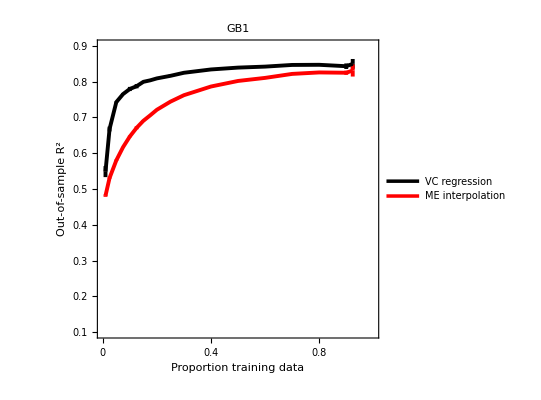

```mathematica
plotVcMe=ListPlot[
Join[plotdatError[[{1}]],{plotdatME}],
BaseStyle->{FontSize->20},
AspectRatio->1,
PlotRange->{{0,1},{.1,.9}},
Frame->True,
PlotStyle->Join[style[[;;1]],{Join[{Red},style[[;;1]][[1,2;;]]]}],
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,Join[modellabs[[;;1]],{Style["ME interpolation",FontFamily->"Helvetica"]}],LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}],
PlotLabel->Style["GB1",Black,FontSize->20]]
```

```mathematica
Export[FileNameJoin[{figpath,"r2_vc_me_GB1.m"}],plotVcMe];
```

#### Scatter plots of predictions

```mathematica
j=1;
```

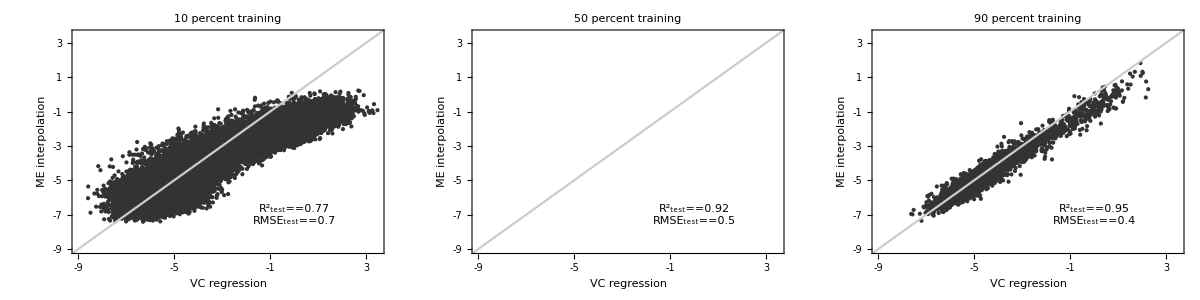

```mathematica
Grid[{Table[ScatterPlot2[pdsVC[[i,j]][[Complement[seqlist,trs[[i,j]]]]],pdsME[[i,j]][[Complement[seqlist,trs[[i,j]]]]],Style[StringJoin[ToString[proportions[[i]]*100//IntegerPart]," percent training"],FontFamily->"Helvetica",FontSize->18],Style["VC regression",FontFamily->"Helvetica",FontSize->18],Style["ME interpolation",FontFamily->"Helvetica",FontSize->18]],{i,{5,13,-2}}]}]
```

```mathematica
Export[FileNameJoin[{figpath,"scatter_vc_me_GB1.pdf"}],%];
```